CompiledFunction[…]

CompiledFunction[…]

Mathe starting

Prestazioni Mathe: 
 Media per singolo frame: 0.112846
 Tempo massimo per singolo frame: 0.118348
 Tempo minimo per singolo frame: 0.109505
 Tempo totale per 10 frame: 1.130461

Simple starting

Prestazioni simple: 
 Media per singolo frame: 1.525444
 Tempo massimo per singolo frame: 1.548702
 Tempo minimo per singolo frame: 1.513573
 Tempo totale per 10 frame: 15.255444

Fast starting

Prestazioni fast: 
 Media per singolo frame: 0.5304605
 Tempo massimo per singolo frame: 0.5405485
 Tempo minimo per singolo frame: 0.5250405
 Tempo totale per 10 frame: 5.3046047

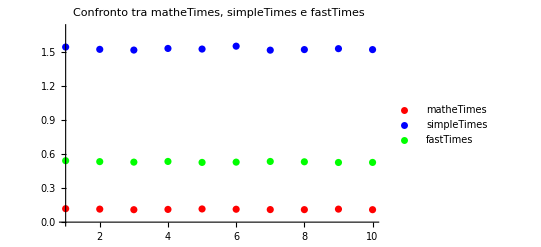

```mathematica
matheFunc[foto_]:=Module[{img,imgBin,imgFilt,imgEnhanced,edges,dilatedEdges,filledImage,componenti,misure},SetDirectory[NotebookDirectory[]];
img=Import[foto];
img=ImageResize[img,Scaled[0.5]];
imgBin=Binarize[img];
imgFilt=GaussianFilter[imgBin,1];
imgEnhanced=ImageAdjust[imgFilt];
edges=EdgeDetect[imgEnhanced];
dilatedEdges=Dilation[edges,DiskMatrix[1]];
filledImage=FillingTransform[dilatedEdges];
componenti=MorphologicalComponents[filledImage];
misure=ComponentMeasurements[componenti,{"Centroid","BoundingBox","Orientation","Shape","Area","PerimeterLength","BoundingBoxArea","Eccentricity","Circularity","Rectangularity"}]]


simpleFunc[foto_]:=Module[{img,imgBin,imgFilt,imgEnhanced,edges,dilatedEdges,filledImage,componenti,misure},SetDirectory[NotebookDirectory[]];
img=Import[foto];
img=ImageResize[img,Scaled[0.5]];
imgBin=simpleBinarize[img];
imgFilt=GaussianFilter[imgBin,1];
imgEnhanced=ImageAdjust[imgFilt];
edges=EdgeDetect[imgEnhanced];
dilatedEdges=simpleDilation[edges,DiskMatrix[1]];
filledImage=simpleFillingTransform[dilatedEdges];
componenti=MorphologicalComponents[filledImage];
misure=ComponentMeasurements[componenti,{"Centroid","BoundingBox","Orientation","Shape","Area","PerimeterLength","BoundingBoxArea","Eccentricity","Circularity","Rectangularity"}]]

simpleBinarize[img_Image]:=Module[{gray,data,thresh,binaryData},gray=ColorConvert[img,"Grayscale"];
data=ImageData[gray];
thresh=Mean[Flatten[data]];
binaryData=Map[If[#>thresh,1,0]&,data,{2}];
Image[binaryData,"Bit"]]

simpleDilation[img_Image,se_?MatrixQ]:=Module[{data,dims,seDims,offset,padded,result},data=ImageData[img];
dims=Dimensions[data];
seDims=Dimensions[se];
offset=Floor[seDims/2];
padded=ArrayPad[data,offset,0];
result=Table[If[Max[padded[[i;;i+seDims[[1]]-1,j;;j+seDims[[2]]-1]]*se]==1,1,0],{i,1,dims[[1]]},{j,1,dims[[2]]}];
Image[result,"Bit"]]

simpleFillingTransform[img_Image]:=Module[{data,dims,compImg,binImg,comp,borderIDs,holeMask,filledData},data=ImageData[img];
dims=Dimensions[data];
compImg=1-data;
binImg=Binarize[Image[compImg]];
comp=MorphologicalComponents[binImg];
borderIDs=DeleteDuplicates[Flatten[{comp[[1,All]],comp[[dims[[1]],All]],comp[[All,1]],comp[[All,dims[[2]]]]}]];
holeMask=Map[If[#!=0&&Not[MemberQ[borderIDs,#]],1,0]&,comp,{2}];
filledData=MapThread[Max[#1,#2]&,{data,holeMask},2];
Image[filledData,"Bit"]]


compiledBinarize=Compile[{{data,_Real,2},{thresh,_Real}},Table[If[data[[i,j]]>thresh,1,0],{i,Length[data]},{j,Length[data[[1]]]}],RuntimeAttributes->{Listable},Parallelization->True]

compiledDilation=Compile[{{data,_Real,2}},Module[{dims,padded,result},dims=Dimensions[data];
padded=ArrayPad[data,1,0];
result=Table[If[Max[padded[[i,j]],padded[[i,j+1]],padded[[i,j+2]],padded[[i+1,j]],padded[[i+1,j+1]],padded[[i+1,j+2]],padded[[i+2,j]],padded[[i+2,j+1]],padded[[i+2,j+2]]]==1,1,0],{i,1,dims[[1]]},{j,1,dims[[2]]}];
result],RuntimeAttributes->{Listable},Parallelization->True]

fastBinarize[img_Image]:=Module[{gray,data,thresh,binaryData},gray=ColorConvert[img,"Grayscale"];
data=ImageData[gray];
thresh=Mean[Flatten[data]];
binaryData=compiledBinarize[data,thresh];
Image[binaryData,"Bit"]]

fastDilation[img_Image]:=Module[{data,result},data=ImageData[img];
result=compiledDilation[data];
Image[result,"Bit"]]

(*Definizione della funzione fastSimpleFunc*)
fastSimpleFunc[foto_]:=Module[{img,imgBin,imgFilt,imgEnhanced,edges,dilatedEdges,filledImage,componenti,misure},SetDirectory[NotebookDirectory[]];
img=Import[foto];
img=ImageResize[img,Scaled[0.5]];
imgBin=fastBinarize[img];
imgFilt=GaussianFilter[imgBin,1];
imgEnhanced=ImageAdjust[imgFilt];
edges=EdgeDetect[imgEnhanced];
dilatedEdges=fastDilation[edges];
filledImage=simpleFillingTransform[dilatedEdges];
componenti=MorphologicalComponents[filledImage];
misure=ComponentMeasurements[componenti,{"Centroid","BoundingBox","Orientation","Shape","Area","PerimeterLength","BoundingBoxArea","Eccentricity","Circularity","Rectangularity"}]]

(*Valutazione delle prestazioni*)
SetDirectory[NotebookDirectory[]];
foto="foto5.jpg";

matheTimes={};
simpleTimes={};
fastTimes={};

Print["Mathe starting"];
tot=AbsoluteTime[];
For[i=0,i<10,i++,time=AbsoluteTime[];
matheFunc[foto];
timer=AbsoluteTime[]-time;
AppendTo[matheTimes,timer];];
totm=AbsoluteTime[]-tot;

Print["Prestazioni Mathe: \n Media per singolo frame: ",Mean[matheTimes],"\n Tempo massimo per singolo frame: ",Max[matheTimes],"\n Tempo minimo per singolo frame: ",Min[matheTimes],"\n Tempo totale per 10 frame: ",totm];

Print["Simple starting"];
tot=AbsoluteTime[];
For[i=0,i<10,i++,times=AbsoluteTime[];
simpleFunc[foto];
timers=AbsoluteTime[]-times;
AppendTo[simpleTimes,timers];];
tots=AbsoluteTime[]-tot;

Print["Prestazioni simple: \n Media per singolo frame: ",Mean[simpleTimes],"\n Tempo massimo per singolo frame: ",Max[simpleTimes],"\n Tempo minimo per singolo frame: ",Min[simpleTimes],"\n Tempo totale per 10 frame: ",tots];

Print["Fast starting"];
tot=AbsoluteTime[];
For[i=0,i<10,i++,timef=AbsoluteTime[];
fastSimpleFunc[foto];
timerf=AbsoluteTime[]-timef;
AppendTo[fastTimes,timerf];];
totf=AbsoluteTime[]-tot;

Print["Prestazioni fast: \n Media per singolo frame: ",Mean[fastTimes],"\n Tempo massimo per singolo frame: ",Max[fastTimes],"\n Tempo minimo per singolo frame: ",Min[fastTimes],"\n Tempo totale per 10 frame: ",totf];

ListPlot[{matheTimes,simpleTimes,fastTimes},PlotLegends->{"matheTimes","simpleTimes","fastTimes"},PlotStyle->{Red,Blue,Green},PlotLabel->"Confronto tra matheTimes, simpleTimes e fastTimes",PlotRange->{{1,10},{0,Max[matheTimes,simpleTimes,fastTimes]*1.1}}]
```